```mathematica
R5=R1;
R6=6R1;
R2=2R1;
R3=3R1;
R4=4R1;
ZL1=L1*s;
ZC1=1/(s*C1);
ZC1L1=Simplify[(ZC1*ZL1)/(ZC1+ZL1)];

Print["ZL1 = ", ZL1]
Print["ZC1 = ",ZC1]
Print["ZC1L1 = ",ZC1L1]
```

```mathematica
(*тут решение узловыми*)
```

```mathematica
(*Дальше начинаются идентичные шаги*)

GL1=IL/Ux;
GC1=UC/Ux;
Gy=Uy/Ux;
Print["GL = ",GL1]
Print["GC = ",GC1]
Print["Gy = ",Gy]
```

GL = 36/(84 R1+73 L1 s+84 C1 L1 R1 s^2)

GC = (36 L1 s)/(84 R1+73 L1 s+84 C1 L1 R1 s^2)

Gy = (3 (12 R1+13 L1 s+12 C1 L1 R1 s^2))/(84 R1+73 L1 s+84 C1 L1 R1 s^2)

```mathematica
(*Решаем уравнение в знаменетеле(Должен быть одинаковым
на токе, выходном напряжении и напряжении конденсатора)
```

```mathematica
sol=Solve[Denominator[Gy]==0,s]
p1=sol[[1,1,2]]/.R1->29/.L1->0.095*10^-3/.C1->9.224*10^-9;
p2=sol[[2,1,2]]/.R1->29/.L1->0.095*10^-3/.C1->9.224*10^-9;
p3=0;
Print["p1 = ",sol[[1,1,2]]," = ",p1]
Print["p2 = ",sol[[2,1,2]]," = ",p2]
Print["p3 = 0"]
```

{{s→(-73 L1-√(5329 L1^2-28224 C1 L1 R1^2))/(168 C1 L1 R1)},{s→(-73 L1+√(5329 L1^2-28224 C1 L1 R1^2))/(168 C1 L1 R1)}}

p1 = (-73 L1-√(5329 L1^2-28224 C1 L1 R1^2))/(168 C1 L1 R1) = -2.84815×10^6

p2 = (-73 L1+√(5329 L1^2-28224 C1 L1 R1^2))/(168 C1 L1 R1) = -400677.

p3 = 0

```mathematica
(*Полюса приравниваем к решениям уравнения.
Третий полюс равен нулю*)
```

```mathematica
(*Сюда вставляется знаменатель умноженный на s*)
```

```mathematica
Dh[s_]:=Denominator[Gy]*s;
```

```mathematica
dDh[s_]:=Expand[D[Dh[s],s]];
(*Тут идут числители характеристик выходного напряжения, тока на индуктивности и напряжения на конденсаторе соответственно*)
```

```mathematica
Ny[s_]=Numerator[Gy];
```

```mathematica
NL1[s_]=Numerator[GL1];
```

```mathematica
NC1[s_]=Numerator[GC1];
(*Дальше шаблонные вычисления*)
```

```mathematica
R1=29;
L1=0.095*10^-3;
C1=9.224*10^-9;
```

```mathematica
h1y=Ny[s]/dDh[s]/.s->p1;h2y=Ny[s]/dDh[s]/.s->p2;h3y=Ny[s]/dDh[s]/.s->p3;
h1C1=NC1[s]/dDh[s]/.s->p1;h2C1=NC1[s]/dDh[s]/.s->p2;h3C1=NC1[s]/dDh[s]/.s->p3;
h1L1=NL1[s]/dDh[s]/.s->p1;h2L1=NL1[s]/dDh[s]/.s->p2;h3L1=NL1[s]/dDh[s]/.s->p3;
Print[TemplateApply["h1y = ``, h2y = ``, h3y = ``",{h1y,h2y,h3y}]]
Print[TemplateApply["h1C1 = ``, h2C1 = ``, h3C1 = ``",{h1C1,h2C1,h3C1}]]
Print[TemplateApply["h1L = ``, h2L = ``, h3L = ``",{h1L1,h2L1,h3L1}]]
(*Ниже продолжение*)
```

h1y = -0.140275, h2y = 0.140275, h3y = 0.428571

h1C1 = -0.654619, h2C1 = 0.654619, h3C1 = 0.0

h1L = 0.00241937, h2L = -0.0171977, h3L = 0.0147783

```mathematica
(*Также без изменений*)
```

```mathematica
hy=h1y*Exp[p1*t]+h2y*Exp[p2*t]+h3y*Exp[p3*t];
graphHC1=h1C1*Exp[p1*t]+h2C1*Exp[p2*t]+h3C1*Exp[p3*t];
```

```mathematica
graphHL1=h1L1*Exp[p1*t]+h2L1*Exp[p2*t]+h3L1*Exp[p3*t];
```

```mathematica
Print["hy(t) = ",hy]
Print["hC(t) = ",graphHC1]
Print["hL(t) = ",graphHL1]
```

hy(t) = 0.428571-0.140275 ⅇ^(-2.84815×10^6 t)+0.140275 ⅇ^(-400677. t)

hC(t) = 0.-0.654619 ⅇ^(-2.84815×10^6 t)+0.654619 ⅇ^(-400677. t)

hL(t) = 0.0147783+0.00241937 ⅇ^(-2.84815×10^6 t)-0.0171977 ⅇ^(-400677. t)

```mathematica
(*Ваши значения из варианта*)
```

```mathematica
R1=27;L1=0.081/1000;C1=12.28/10^9;
(*PlotRange и GridLines могут отличаться от варианта к варианту.
Подбирайте экспериментально*)
```

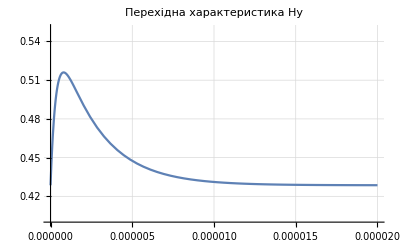

```mathematica
Plot[hy,{t,0,2*10^-5},PlotRange->{0.4,0.55},GridLines->Automatic,PlotLabel->HoldForm[Перехідна характеристика Hy]]
```

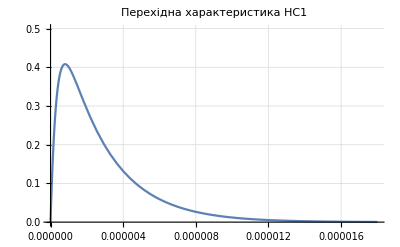

```mathematica
Plot[graphHC1,{t,0,1.8*10^-5},PlotRange->{0,0.5},GridLines->Automatic,PlotLabel->HoldForm[Перехідна характеристика HC1]]
```

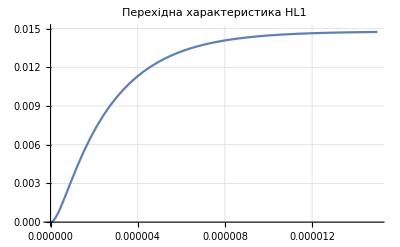

```mathematica
Plot[graphHL1,{t,0,1.5*10^-5},PlotRange->{0,0.015},GridLines->Automatic,PlotLabel->HoldForm[Перехідна характеристика HL1]]
```